```mathematica
$Assumptions = {x ∈ Reals, y ∈ Reals, λ ∈ Reals, κ ∈ Reals, v1 ∈ Reals, v2 ∈ Reals}
```

{x∈ℝ,y∈ℝ,λ∈ℝ,κ∈ℝ,v1∈ℝ,v2∈ℝ}

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
κ1 = FullSimplify[κ]
κ3 = FullSimplify[κ ω]
κ5 = FullSimplify[κ Conjugate[ω]]
```

κ

(-1)^(2/3) κ

-(-1)^(1/3) κ

## Uniform potential analysis

```mathematica
unishit = FullSimplify[ComplexExpand[1/Sqrt[1 + λ^2 (κ3 + x + I y)Conjugate[(κ3 + x + I y) ]]*1/Sqrt[1 + λ^2 (κ5 + x + I y)Conjugate[(κ5 + x + I y) ]]*(1 + λ^2 (Conjugate[κ3] + x - I y) (κ5 + x + I y)), {κ3, κ5}]]
```

(2+(2 (x^2+y^2)+(-2-2 ⅈ √3) x κ+ⅈ (ⅈ+√3) κ^2) λ^2)/(2 √(1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4))

```mathematica
temp=D[unishit,x]
x=0
y=0
α = FullSimplify[temp]
```

-(((2+(2 (x^2+y^2)+(-2-2 ⅈ √3) x κ+ⅈ (ⅈ+√3) κ^2) λ^2) (2 (2 x-κ) λ^2+(4 x (x^2+y^2)-4 x^2 κ-2 (x^2+y^2) κ+6 x κ^2-2 κ^3) λ^4))/(4 (1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4)^(3/2)))+((4 x+(-2-2 ⅈ √3) κ) λ^2)/(2 √(1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4))

0

0

-(ⅈ (2 √3 κ λ^2+(-3 ⅈ+√3) κ^3 λ^4))/(2 (1+κ^2 λ^2)^2)

```mathematica
FullSimplify[α - (-I Sqrt[3]/((1 + κ^2 λ^2)^2)*κ λ^2 * (1 - ω κ^2 λ^2))]
```

0

```mathematica
Clear[x,y]
```

## Linear Potential analysis

```mathematica
antishit = FullSimplify[ComplexExpand[1/Sqrt[1 + λ^2 (κ3 + x + I y)Conjugate[(κ3 + x + I y) ]]*1/Sqrt[1 + λ^2 (κ5 + x + I y)Conjugate[(κ5 + x + I y) ]]*(1 - λ^2 (Conjugate[κ3] + x - I y) (κ5 + x + I y)), {κ3, κ5}]]
```

(2+(-2 (x^2+y^2)+(2+2 ⅈ √3) x κ+(1-ⅈ √3) κ^2) λ^2)/(2 √(1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4))

```mathematica
temp=D[antishit,x]
x=0
y=0
α = FullSimplify[temp]
```

-(((2+(-2 (x^2+y^2)+(2+2 ⅈ √3) x κ+(1-ⅈ √3) κ^2) λ^2) (2 (2 x-κ) λ^2+(4 x (x^2+y^2)-4 x^2 κ-2 (x^2+y^2) κ+6 x κ^2-2 κ^3) λ^4))/(4 (1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4)^(3/2)))+((-4 x+(2+2 ⅈ √3) κ) λ^2)/(2 √(1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4))

0

0

(κ λ^2 (4+2 ⅈ √3+(3+ⅈ √3) κ^2 λ^2))/(2 (1+κ^2 λ^2)^2)

```mathematica
FullSimplify[α - κ λ^2/((1 + κ^2 λ^2)^2) (2 + I Sqrt[3] (1 - λ^2 κ^2 ω))]
```

0

```mathematica
Clear[x,y]
```

```mathematica
vec =FullSimplify[ 1/Sqrt[1 + λ^2 (x^2+ y^2)] {1, λ (x + I y)}]
```

{1/(√(1+(x^2+y^2) λ^2)),((x+ⅈ y) λ)/(√(1+(x^2+y^2) λ^2))}

```mathematica
Ω = FullSimplify[ComplexExpand[-2 Im[Conjugate[D[vec, x]].D[vec,y]]]]
```

-(2 λ^2)/((1+(x^2+y^2) λ^2)^2)

```mathematica
x = κ
y=0
FullSimplify[Ω]
```

κ

0

-(2 λ^2)/((1+κ^2 λ^2)^2)

```mathematica
FullSimplify[unishit]
```

(2+(-1-ⅈ √3) κ^2 λ^2)/(2+2 κ^2 λ^2)

```mathematica
FullSimplify[Solve[Arg[unishit]==-π/3, λ]]
```

{{λ→-1/Abs[κ]},{λ→1/Abs[κ]}}

```mathematica
FullSimplify[ComplexExpand[Arg[unishit]]]
```

Arg[2+(-1-ⅈ √3) κ^2 λ^2]

## General Potential

```mathematica
genshit = FullSimplify[ComplexExpand[1/Sqrt[1 + λ^2 (κ3 + x + I y)Conjugate[(κ3 + x + I y) ]]*1/Sqrt[1 + λ^2 (κ5 + x + I y)Conjugate[(κ5 + x + I y) ]]*(v1 + v2 * λ^2 (Conjugate[κ3] + x - I y) (κ5 + x + I y)), {κ3, κ5}]]
```

(2 v1+v2 (2 (x^2+y^2)+(-2-2 ⅈ √3) x κ+ⅈ (ⅈ+√3) κ^2) λ^2)/(2 √(1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4))

```mathematica
Clear[x,y]
temp=D[genshit,x]
x=0
y=0
α = FullSimplify[temp]
```

-(((2 v1+v2 (2 (x^2+y^2)+(-2-2 ⅈ √3) x κ+ⅈ (ⅈ+√3) κ^2) λ^2) (2 (2 x-κ) λ^2+(4 x (x^2+y^2)-4 x^2 κ-2 (x^2+y^2) κ+6 x κ^2-2 κ^3) λ^4))/(4 (1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4)^(3/2)))+(v2 (4 x+(-2-2 ⅈ √3) κ) λ^2)/(2 √(1+2 (x^2+y^2-x κ+κ^2) λ^2+((x^2+y^2)^2-2 x (x^2+y^2) κ+(3 x^2-y^2) κ^2-2 x κ^3+κ^4) λ^4))

0

0

(κ λ^2 (2 v1+v2 (-2-2 ⅈ √3+(-3-ⅈ √3) κ^2 λ^2)))/(2 (1+κ^2 λ^2)^2)

```mathematica
Δ = FullSimplify[genshit]
```

(2 v1+ⅈ (ⅈ+√3) v2 κ^2 λ^2)/(2+2 κ^2 λ^2)

```mathematica
v1 = -1
v2 = -1
κ=1
FullSimplify[ComplexExpand[Series[Abs[Δ]/Abs[α], {λ, 1, 2}]],Assumptions->κ>0]
```

-1

-1

1

2/3-(2 (λ-1))/3+17/9 (λ-1)^2+O[λ-1]^3

```mathematica
Clear[λ]
```

```mathematica
v1=-1
v2=-1
κ=1
FullSimplify[Abs[Δ]/Abs[α]]
```

-1

-1

1

(1+λ^6)/(√3 λ^2 √(1+λ^4+λ^8))

```mathematica
FullSimplify[NSolve[D[(1+λ^6)/(√3 λ^2 √(1+λ^4+λ^8)), λ]==0, λ]]
```

{{λ→1.59588},{λ→-1.59588},{λ→0.420242-0.67083 ⅈ},{λ→0.420242+0.67083 ⅈ},{λ→-0.420242-0.67083 ⅈ},{λ→-0.420242+0.67083 ⅈ}}

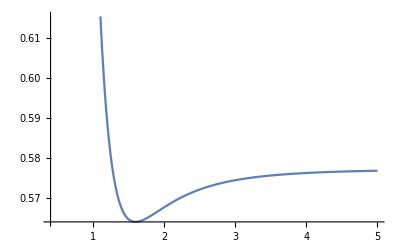

```mathematica
Plot[Abs[Δ]/Abs[α], {λ, 0.4, 5}]
```

```mathematica
FullSimplify[Limit[Abs[Δ]/Abs[α], λ->Infinity]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/(√3)

```mathematica
Clear[κ]
```

```mathematica
v1=-1
v2=-1
FullSimplify[Abs[Δ]/Abs[α]]
```

-1

-1

(1+κ^6)/(√3 √(1+κ^4+κ^8) Abs[κ])

```mathematica
λ=1/κ
FullSimplify[Solve[κ/2 == (4 Abs[Δ]/2 v)/(3 Abs[α]^2/4+4 Abs[α]/2 v), v]]
```

1/κ

Solve::fdimc: When parameter values satisfy the condition κ==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{v→27/(32 (4 κ-3 Abs[κ]))}}

```mathematica
N[27/160]
```

0.16875

```mathematica
Clear[κ]
```